# A billiard ball as a point reflected elastically inside a region

Define a region
Discretizes the region into a MeshRegion. 
Then given its boundary edge indices, find all boundary edges
Given a point on one of the edges, define a direction and a ray (green line)
Find the first edge that the ray intersect
Given the intersection point, find the reflection by considering the edge at the intersection point
Repeat this process

## Ball confined in a Stadium

```mathematica
η=0;
p1={Sin[x]+η,Cos[x]}/.NSolve[ArcLength[{Sin[θ],Cos[θ]},{θ,0,x}]==1,x][[1]]
α0=y/.NSolve[{Cos[y]==1/ⅇ,0<=y<=π}][[1]]
(α0/π)180.
Clear[x,y,θ]
```

{0.841471,0.540302}

1.19407

68.4151

Define a region:

```mathematica
reg= StadiumShape[{{0,0},{η,0}},1];
```

Find all of its boundary edges:

```mathematica
edges=boundaryEdges[reg,MaxCellMeasure->{"Length"->.05}];
```

From boundary edges, pick one randomly and one point within that:

```mathematica
(*edge1=RandomChoice[edges];
p1=Mean@@edge1;*)
```

{{x→1.}}

{{α0→1.19407}}

```mathematica
edge1=MinimalBy[edges,RegionDistance[#,p1]&][[1]]
```

Line[{{0.85186,0.51994},{0.833998,0.551768}}]

```mathematica
Graphics[{{Opacity[.3],DiscretizeRegion@reg},{Red,PointSize[Medium],Point[p1]},{Green,ray1=HalfLine[p1,-{Sin[α0],Cos[α0]}],edge1}}]
```

-Graphics-

From the initial point, pick a ray in a given direction
Make sure the ray does not go outside of the region

```mathematica
(*Manipulate[Graphics[{{Opacity[.3],DiscretizeRegion@reg},{Red,PointSize[Medium],Point[p1]},{Green,Dynamic[ray1=HalfLine[p1,pnt2-p1]]}}],{{pnt2,Mean@@RandomChoice[edges]},Locator}]*)
```

Given initial edge, point, and ray, find all 200 reflections within the region:

```mathematica
final=NestList[reflect[#,edges]&,{p1,edge1,ray1},10^3];//AbsoluteTiming
```

{53.6106,Null}

Find all rays reflected within the region:

```mathematica
lines=Line/@Partition[final[[All,1]],2,1];
```

Visualize them:

```mathematica
Manipulate[Graphics[{{edges,Opacity[.2],LightBlue,DiscretizeRegion@reg},{Green,PointSize[Medium],Point[final[[1,1]]]},{Red,Opacity[.2],lines[[;;st]]},{Blue,lines[[st]]}}],{st,1,Length[lines],1}]
```

```mathematica
origin={η+1,0};
pnts=SortBy[DeleteDuplicates[Join[Flatten[boundaryEdges[reg][[All,1]],1],{origin},final[[All,1]]]],ArcTan[Sequence@@#]&];
pnts=RotateLeft[pnts,Position[pnts,origin][[1,1]]-1];
```

Since there is not collision for the last point and also first point, then for arc length calculations, we will not consider them:

```mathematica
s=ArcLength[Line@pnts[[;;Position[pnts,#][[1,1]]]]]&/@final[[2;;-2,1]];
ℒ=ArcLength[Line@pnts];
```

```mathematica
collision=Partition[final[[All,1]],3,1];
```

```mathematica
θ=1/2(Module[{q1,p,q2},
{q1,p,q2}=#;Sign[Cross[Append[0][p-q1],Append[0][q2-p]][[-1]]]]PlanarAngle[#])&/@collision;
```

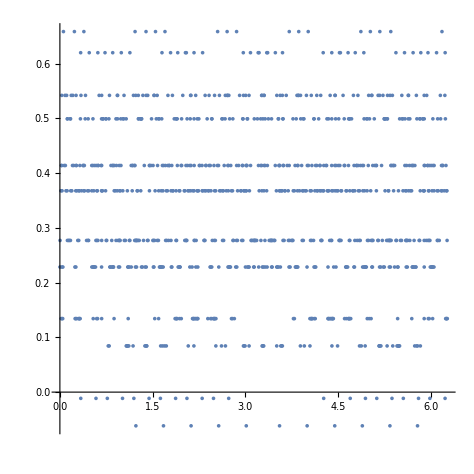

```mathematica
ListPlot[Transpose[{s,Sin[θ]}],AspectRatio->1,PlotRange->All]
```

```mathematica
Transpose[{s/ℒ,Sin[θ]}][[;;2]]
```

{{0.567009,0.122761},{0.161434,0.669642}}

```mathematica
Manipulate[
inc=pnts[[;;Position[pnts,final[[st+1,1]]][[1,1]]]];
Row@{Graphics[{{edges,Opacity[.2],LightBlue,DiscretizeRegion@reg},{Green,PointSize[Large],Point[origin],Line[inc]},{Red,PointSize[Medium],Point[final[[1,1]]]},{Red,lines[[;;st]],Blue,Arrow[{final[[st,1]],final[[st+1,1]]}],Arrow[{final[[st+1,1]],final[[st+2,1]]}]}},ImageSize->Small],ListPlot[Transpose[{s/ℒ,Sin[θ]}][[;;st]]->Range[st],AspectRatio->1,PlotRange->{{0,1},{-1,1}},Frame->True,GridLines->Automatic,ImageSize->Small](*,{#,#[[2]]<0,Sin[#[[2]]]}&/@(Transpose[{s/ℒ,θ}][[;;st]])*)},{st,1,100,1}]
```

Part::partd: Part specification final[[18,1]] is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::span: 1 ;; {}[[1,1]] is not a valid Span specification. A Span
     specification should be 1, 2, or 3 machine-sized integers separated by
     ;;. (Any of the integers can be omitted or replaced with All.)

DiscretizeRegion::regp: 
   A correctly specified region expected at position 1 of 
    DiscretizeRegion[reg].

Part::partd: Part specification final[[1,1]] is longer than depth of object.

Part::take: Cannot take positions 1 through 17 in lines.

Part::partd: Part specification final[[17,1]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Transpose::nmtx: 
                             3.32096  5.92661  2.19951  5.00424  1.66143
   The first two levels of {{-------, -------, -------, -------, -------, 
                                ℒ        ℒ        ℒ        ℒ        ℒ
      4.66672  1.12251  3.74545  0.000951284  2.82282  5.74077  2.48526
      -------, -------, -------, -----------, -------, -------, -------, 
         ℒ        ℒ        ℒ          ℒ          ℒ        ℒ        ℒ
               4.9437  1.72181  4.60599  1.18395  4.26816  1.22965
      <<981>>, ------, -------, -------, -------, -------, -------}, Sin[θ]}
                 ℒ        ℒ        ℒ        ℒ        ℒ        ℒ
     cannot be transposed.

Part::take: Cannot take positions 1 through 17 in 
                3.32096  5.92661  2.19951  5.00424  1.66143  4.66672
    Transpose[{{-------, -------, -------, -------, -------, -------, 
                   ℒ        ℒ        ℒ        ℒ        ℒ        ℒ
       1.12251  3.74545  0.000951284  2.82282  5.74077           4.9437
       -------, -------, -----------, -------, -------, <<982>>, ------, 
          ℒ        ℒ          ℒ          ℒ        ℒ                ℒ
       1.72181  4.60599  1.18395  4.26816  1.22965
       -------, -------, -------, -------, -------}, Sin[θ]}].
          ℒ        ℒ        ℒ        ℒ        ℒ

Part::pkspec1: The expression Charting`ChartLabelingDump`getLength[1 ;; 17]
     cannot be used as a part specification.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression Annotation[1 ;; 17, Charting`Private`Tag#2]
     cannot be used as a part specification.

General::stop: Further output of Part::pkspec1
     will be suppressed during this calculation.

3.32096  5.92661  2.19951  5.00424
ListPlot::lpn: Annotation[Transpose[{{-------, -------, -------, -------, 
                                         ℒ        ℒ        ℒ        ℒ
         1.66143  4.66672  1.12251  3.74545  0.000951284           <<7>>
         -------, -------, -------, -------, -----------, <<985>>, -----, 
            ℒ        ℒ        ℒ        ℒ          ℒ                  ℒ
         4.60599  1.18395  4.26816  1.22965
         -------, -------, -------, -------}, <<1>>}], Ch<<19>>1][[<<1>>]] is
            ℒ        ℒ        ℒ        ℒ
     not a list of numbers or pairs of numbers.

Part::partd: Part specification final[[18,1]] is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::span: 1 ;; {}[[1,1]] is not a valid Span specification. A Span
     specification should be 1, 2, or 3 machine-sized integers separated by
     ;;. (Any of the integers can be omitted or replaced with All.)

DiscretizeRegion::regp: 
   A correctly specified region expected at position 1 of 
    DiscretizeRegion[reg].

Part::partd: Part specification final[[1,1]] is longer than depth of object.

Part::take: Cannot take positions 1 through 17 in lines.

Part::partd: Part specification final[[17,1]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Transpose::nmtx: 
                             3.32096  5.92661  2.19951  5.00424  1.66143
   The first two levels of {{-------, -------, -------, -------, -------, 
                                ℒ        ℒ        ℒ        ℒ        ℒ
      4.66672  1.12251  3.74545  0.000951284  2.82282  5.74077  2.48526
      -------, -------, -------, -----------, -------, -------, -------, 
         ℒ        ℒ        ℒ          ℒ          ℒ        ℒ        ℒ
               4.9437  1.72181  4.60599  1.18395  4.26816  1.22965
      <<981>>, ------, -------, -------, -------, -------, -------}, Sin[θ]}
                 ℒ        ℒ        ℒ        ℒ        ℒ        ℒ
     cannot be transposed.

Part::take: Cannot take positions 1 through 17 in 
                3.32096  5.92661  2.19951  5.00424  1.66143  4.66672
    Transpose[{{-------, -------, -------, -------, -------, -------, 
                   ℒ        ℒ        ℒ        ℒ        ℒ        ℒ
       1.12251  3.74545  0.000951284  2.82282  5.74077           4.9437
       -------, -------, -----------, -------, -------, <<982>>, ------, 
          ℒ        ℒ          ℒ          ℒ        ℒ                ℒ
       1.72181  4.60599  1.18395  4.26816  1.22965
       -------, -------, -------, -------, -------}, Sin[θ]}].
          ℒ        ℒ        ℒ        ℒ        ℒ

Part::pkspec1: The expression Charting`ChartLabelingDump`getLength[1 ;; 17]
     cannot be used as a part specification.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression Annotation[1 ;; 17, Charting`Private`Tag#2]
     cannot be used as a part specification.

General::stop: Further output of Part::pkspec1
     will be suppressed during this calculation.

3.32096  5.92661  2.19951  5.00424
ListPlot::lpn: Annotation[Transpose[{{-------, -------, -------, -------, 
                                         ℒ        ℒ        ℒ        ℒ
         1.66143  4.66672  1.12251  3.74545  0.000951284           <<7>>
         -------, -------, -------, -------, -----------, <<985>>, -----, 
            ℒ        ℒ        ℒ        ℒ          ℒ                  ℒ
         4.60599  1.18395  4.26816  1.22965
         -------, -------, -------, -------}, <<1>>}], Ch<<19>>1][[<<1>>]] is
            ℒ        ℒ        ℒ        ℒ
     not a list of numbers or pairs of numbers.

```mathematica
ListPlot[Transpose[{s/ℒ,Sin[θ]}][[;;st]]->Range[st],AspectRatio->1,PlotRange->{{0,1},{-1,1}},Frame->True,GridLines->Automatic,ImageSize->Medium]
```

-Graphics-

### scratch paper

```mathematica
(*angle[step_]:=Module[{l,hl,q2,p,q1},
{l,hl}=Rest@step;
q2=l[[1,1]];p=hl[[1]];q1=hl[[1]]+hl[[2]];
PlanarAngle[p->{q1,q2}]]*)
```

```mathematica
Rationalize[angle[final[[2]]]/π,.01]
```

2/7

```mathematica
PlanarAngle[Partition[final[[All,1]],3,1][[1]]]/π/2
```

0.210338

```mathematica
step=final[[2]];
Graphics[{{edges,Opacity[.2],LightBlue,DiscretizeRegion@reg},{Blue,final[[1,-1]]},{Green,PointSize[Medium],Point@step[[1]]},{Red,step[[2;;]]}}]
```

-Graphics-

```mathematica
pnts=SortBy[DeleteDuplicates[Join[Flatten[boundaryEdges[reg][[All,1]],1],{origin},final[[All,1]]]],ArcTan[Sequence@@#]&];
pnts=RotateLeft[pnts,Position[pnts,origin][[1,1]]-1];
```

```mathematica
ArcLength[Line@pnts[[;;Position[pnts,final[[10,1]]][[1,1]]]]]
```

8.10974

```mathematica
MeshPrimitives[BoundaryDiscretizeRegion[StadiumShape[]],1]
```

{Line[{{1.,-1.},{1.14231,-0.989821}}],Line[{{1.14231,-0.989821},{1.28173,-0.959493}}],Line[{{1.28173,-0.959493},{1.41542,-0.909632}}],Line[{{1.41542,-0.909632},{1.54064,-0.841254}}],Line[{{1.54064,-0.841254},{1.65486,-0.75575}}],Line[{{1.65486,-0.75575},{1.75575,-0.654861}}],Line[{{1.75575,-0.654861},{1.84125,-0.540641}}],Line[{{1.84125,-0.540641},{1.90963,-0.415415}}],Line[{{1.90963,-0.415415},{1.95949,-0.281733}}],Line[{{1.95949,-0.281733},{1.98982,-0.142315}}],Line[{{1.98982,-0.142315},{2.,0.}}],Line[{{2.,0.},{1.98982,0.142315}}],Line[{{1.98982,0.142315},{1.95949,0.281733}}],Line[{{1.95949,0.281733},{1.90963,0.415415}}],Line[{{1.90963,0.415415},{1.84125,0.540641}}],Line[{{1.84125,0.540641},{1.75575,0.654861}}],Line[{{1.75575,0.654861},{1.65486,0.75575}}],Line[{{1.65486,0.75575},{1.54064,0.841254}}],Line[{{1.54064,0.841254},{1.41542,0.909632}}],Line[{{1.41542,0.909632},{1.28173,0.959493}}],Line[{{1.28173,0.959493},{1.14231,0.989821}}],Line[{{1.14231,0.989821},{1.,1.}}],Line[{{1.,1.},{-1.,1.}}],Line[{{-1.,1.},{-1.14231,0.989821}}],Line[{{-1.14231,0.989821},{-1.28173,0.959493}}],Line[{{-1.28173,0.959493},{-1.41542,0.909632}}],Line[{{-1.41542,0.909632},{-1.54064,0.841254}}],Line[{{-1.54064,0.841254},{-1.65486,0.75575}}],Line[{{-1.65486,0.75575},{-1.75575,0.654861}}],Line[{{-1.75575,0.654861},{-1.84125,0.540641}}],Line[{{-1.84125,0.540641},{-1.90963,0.415415}}],Line[{{-1.90963,0.415415},{-1.95949,0.281733}}],Line[{{-1.95949,0.281733},{-1.98982,0.142315}}],Line[{{-1.98982,0.142315},{-2.,0.}}],Line[{{-2.,0.},{-1.98982,-0.142315}}],Line[{{-1.98982,-0.142315},{-1.95949,-0.281733}}],Line[{{-1.95949,-0.281733},{-1.90963,-0.415415}}],Line[{{-1.90963,-0.415415},{-1.84125,-0.540641}}],Line[{{-1.84125,-0.540641},{-1.75575,-0.654861}}],Line[{{-1.75575,-0.654861},{-1.65486,-0.75575}}],Line[{{-1.65486,-0.75575},{-1.54064,-0.841254}}],Line[{{-1.54064,-0.841254},{-1.41542,-0.909632}}],Line[{{-1.41542,-0.909632},{-1.28173,-0.959493}}],Line[{{-1.28173,-0.959493},{-1.14231,-0.989821}}],Line[{{-1.14231,-0.989821},{-1.,-1.}}],Line[{{-1.,-1.},{1.,-1.}}]}

```mathematica
dg=BoundaryDiscretizeRegion[StadiumShape[]];
```

```mathematica
MeshCellIndex[dg,1]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30},{1,31},{1,32},{1,33},{1,34},{1,35},{1,36},{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46}}

```mathematica
lines=MeshPrimitives[dg,1];
```

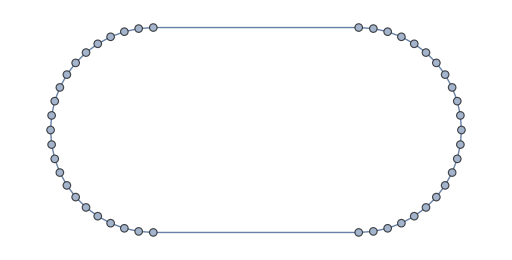

```mathematica
MeshConnectivityGraph[dg,0]
```

{{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30}}

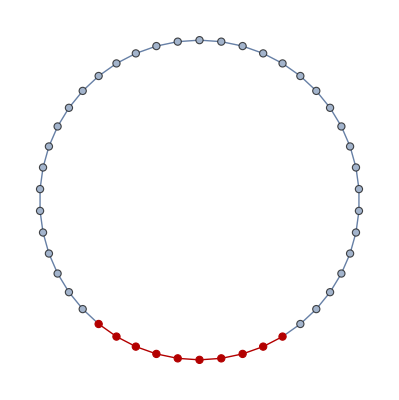

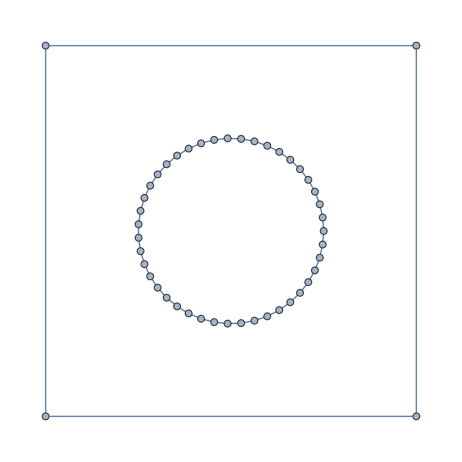

```mathematica
FindShortestPath[MeshConnectivityGraph[dg,1],{1,21},{1,30}]
HighlightGraph[MeshConnectivityGraph[dg,1],PathGraph[%]]
```

```mathematica
boundaryedgeindices=Flatten@Position[Length/@dg["ConnectivityMatrix"[1,2]]["AdjacencyLists"],1];
MeshPrimitives[dg,{1,boundaryedgeindices}]
```

```mathematica
dg["ConnectivityMatrix"]
```

MeshRegion::argnum: -- Message text not found -- (…)

Removed[$$Failure]

## Initializations

Given a region, first discretizes a region reg into a MeshRegion. Then given its boundary edge indices, find all boundary edges, which will be a collection of lines

```mathematica
ClearAll[boundaryEdges];
boundaryEdges[reg_,opts:OptionsPattern[]]:=
Module[{dg,boundaryedgeindices},
dg=DiscretizeRegion[reg,FilterRules[{opts}, Options[DiscretizeRegion]]];
boundaryedgeindices=Flatten@Position[Length/@dg["ConnectivityMatrix"[1,2]]["AdjacencyLists"],1];
MeshPrimitives[dg,{1,boundaryedgeindices}]]
```

Given an initial point, edge and ray, find the reflection inside a region with its given boundary edges. The result will be the next point on edges, its corresponding edge element and ray reflected from that point

```mathematica
ClearAll[reflect];
reflect[{p1_,edge1_,ray1_},boundaryedges_]:=Module[
{boundaryLines,edge2,p2,reflectedP1,ray2},
boundaryLines=Complement[boundaryedges,{edge1}];
{edge2,{p2}}=SortBy[DeleteCases[{#,Graphics`Mesh`FindIntersections[{#,ray1}]}&/@boundaryLines,{_,{}}],Abs[#[[-1,1]]-p1]&][[1]];
reflectedP1=ReflectionTransform[Subtract@@edge2[[1]],p2][p1];
ray2=HalfLine[p2,Subtract@@{reflectedP1,p2}];
{p2,edge2,ray2}
]
```